```mathematica
<<MASSToolbox`Style`
<<MASSToolbox`
```

```mathematica
SetDirectory[NotebookDirectory[]];
glycolysis=Import["../../models/SB2/glycolysis.m.gz"];
ppp=Import["../../models/SB2/ppp.m.gz"];
salvage=Import["../../models/SB2/salvage.m.gz"];
```

```mathematica
glycolysis=ExampleData[{"MASSToolbox","Glycolysis"}];
ppp=ExampleData[{"MASSToolbox","PentosePhosphatePathway"}];
salvage=ExampleData[{"MASSToolbox","NucleotideSalvagePathway"}];
```

```mathematica
combi=Union[glycolysis,ppp,salvage];
(*combi=addSinks[combi];*)
```

```mathematica
getExchanges/@{glycolysis,ppp,salvage}
```

{{(amp^c⇌∅)^vamp,(pyr^c⇌∅)^vpyr,(lac^c⇌∅)^vlac,(∅⇌glu^c)^vgluin,(∅⇌amp^c)^vampin,(h^c⇌∅)^vh,(h2o^c⇌∅)^vh2o},{(co2^c⇌∅)^vco2,(g6p^c⇌∅)^EX_g6p_c,(f6p^c⇌∅)^EX_f6p_c,(r5p^c⇌∅)^EX_r5p_c,(h^c⇌∅)^EX_h_c,(h2o^c⇌∅)^EX_h2o_c,(gap^c⇌∅)^EX_gap_c},{(ade^c⇌∅)^vade,(ado^c⇌∅)^vado,(hyp^c⇌∅)^vhyp,(ino^c⇌∅)^vino,(nh3^c⇌∅)^vnh3,(phos^c⇌∅)^vphos,(amp^c⇌∅)^vamp,(h^c⇌∅)^vh,(h2o^c⇌∅)^vh2o}}

```mathematica
combi=deleteReactions[combi,{"EX_g6p_c","EX_f6p_c","EX_gap_c","EX_h_c","EX_h2o_c","EX_r5p_c"}];
```

```mathematica
combi//Dimensions
```

{40,48}

```mathematica
combi["InitialConditions"]
```

{glu^c→1. Millimole Liter^-1,fdp^c→0.0146 Millimole Liter^-1,dhap^c→0.16 Millimole Liter^-1,pg13^c→0.000243 Millimole Liter^-1,pg3^c→0.0773 Millimole Liter^-1,pg2^c→0.0113 Millimole Liter^-1,pep^c→0.017 Millimole Liter^-1,pyr^c→0.060301 Millimole Liter^-1,lac^c→1.36 Millimole Liter^-1,nad^c→0.0589 Millimole Liter^-1,nadh^c→0.0301 Millimole Liter^-1,v_vhk→1.12 Millimole Hour^-1 Liter^-1,v_vpgi→1.12 Millimole Hour^-1 Liter^-1,v_vpfk→1.12 Millimole Hour^-1 Liter^-1,v_vtpi→1.12 Millimole Hour^-1 Liter^-1,v_vald→1.12 Millimole Hour^-1 Liter^-1,v_vgapdh→2.24 Millimole Hour^-1 Liter^-1,v_vpgk→2.24 Millimole Hour^-1 Liter^-1,v_vpglm→2.24 Millimole Hour^-1 Liter^-1,v_veno→2.24 Millimole Hour^-1 Liter^-1,v_vpk→2.24 Millimole Hour^-1 Liter^-1,v_vldh→2.016 Millimole Hour^-1 Liter^-1,v_vapk→0. Millimole Hour^-1 Liter^-1,v_vpyr→0.224 Millimole Hour^-1 Liter^-1,v_vlac→2.016 Millimole Hour^-1 Liter^-1,v_vatp→2.24 Millimole Hour^-1 Liter^-1,v_vnadh→0.224 Millimole Hour^-1 Liter^-1,v_vgluin→1.12 Millimole Hour^-1 Liter^-1,v_vampin→0.014 Millimole Hour^-1 Liter^-1,g6p^c→0.0486 Millimole Liter^-1,f6p^c→0.0198 Millimole Liter^-1,gap^c→0.00728 Millimole Liter^-1,gl6p^c→0.00175424 Millimole Liter^-1,go6p^c→0.0374753 Millimole Liter^-1,ru5p^c→0.00493679 Millimole Liter^-1,x5p^c→0.0147842 Millimole Liter^-1,s7p^c→0.023988 Millimole Liter^-1,e4p^c→0.00507507 Millimole Liter^-1,nadp^c→0.0002 Millimole Liter^-1,nadph^c→0.0658 Millimole Liter^-1,gsh^c→3.2 Millimole Liter^-1,gssg^c→0.12 Millimole Liter^-1,co2^c→1. Millimole Liter^-1,v_vg6pdh→0.21 Millimole Hour^-1 Liter^-1,v_vpglase→0.21 Millimole Hour^-1 Liter^-1,v_vgl6pdh→0.21 Millimole Hour^-1 Liter^-1,v_vr5pe→0.133333 Millimole Hour^-1 Liter^-1,v_vr5pi→0.0766667 Millimole Hour^-1 Liter^-1,v_vtki→0.0666667 Millimole Hour^-1 Liter^-1,v_vtkii→0.0666667 Millimole Hour^-1 Liter^-1,v_vtala→0.0666667 Millimole Hour^-1 Liter^-1,v_vgssgr→0.42 Millimole Hour^-1 Liter^-1,v_vgshr→0.42 Millimole Hour^-1 Liter^-1,v_vco2→0.21 Millimole Hour^-1 Liter^-1,r5p^c→0.00494 Millimole Liter^-1,ade^c→0.001 Millimole Liter^-1,ado^c→0.0012 Millimole Liter^-1,imp^c→0.01 Millimole Liter^-1,ino^c→0.001 Millimole Liter^-1,hyp^c→0.002 Millimole Liter^-1,r1p^c→0.06 Millimole Liter^-1,prpp^c→0.005 Millimole Liter^-1,amp^c→0.0867281 Millimole Liter^-1,adp^c→0.29 Millimole Liter^-1,atp^c→1.6 Millimole Liter^-1,phos^c→2.5 Millimole Liter^-1,h^c→0.0000630957 Millimole Liter^-1,h2o^c→1. Millimole Liter^-1,nh3^c→0.091 Millimole Liter^-1,v_vak→0.12 Millimole Hour^-1 Liter^-1,v_vampase→0.12 Millimole Hour^-1 Liter^-1,v_vampda→0.014 Millimole Hour^-1 Liter^-1,v_vimpase→0.014 Millimole Hour^-1 Liter^-1,v_vada→0.01 Millimole Hour^-1 Liter^-1,v_vpnpase→0.014 Millimole Hour^-1 Liter^-1,v_vprm→0.014 Millimole Hour^-1 Liter^-1,v_vatpgen→0.148 Millimole Hour^-1 Liter^-1,v_vprppsyn→0.014 Millimole Hour^-1 Liter^-1,v_vadprt→0.014 Millimole Hour^-1 Liter^-1,v_vado→-0.01 Millimole Hour^-1 Liter^-1,v_vade→-0.014 Millimole Hour^-1 Liter^-1,v_vino→0.01 Millimole Hour^-1 Liter^-1,v_vhyp→0.014 Millimole Hour^-1 Liter^-1,v_vamp→0. Millimole Hour^-1 Liter^-1,v_vh→0. Millimole Hour^-1 Liter^-1,v_vh2o→-0.024 Millimole Hour^-1 Liter^-1,v_vphos→0. Millimole Hour^-1 Liter^-1,v_vnh3→0.024 Millimole Hour^-1 Liter^-1}

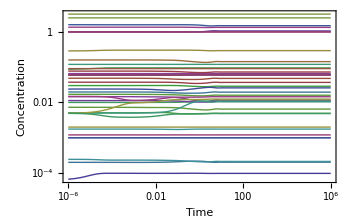

```mathematica
plotSimulation[simulate[combi,{t,0,1000000}][[1]],FrameLabel->{"Time","Concentration"}]
```

```mathematica
combiRelaxed=combi;
updateInitialConditions[combiRelaxed,Flatten[findSteadyState[combi]]]
```

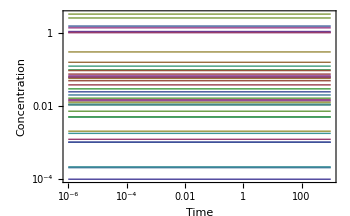

```mathematica
plotSimulation[simulate[combiRelaxed,{t,0,1000}][[1]],FrameLabel->{"Time","Concentration"}]
```

```mathematica
comparisonPlot=Show[ListPlot[Thread[Tooltip[#[[All,2]],#[[All,1]]]],FrameLabel->{"GlycPPPsalvage","Glycolysis"}],Graphics[{Dashed,Line[{{Min[#[[All,2]]],Min[#[[All,2]]]},{Max[#[[All,2]]],Max[#[[All,2]]]}}]}],PlotRange->Automatic]&;
```

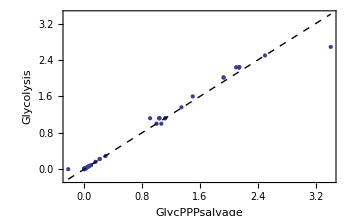

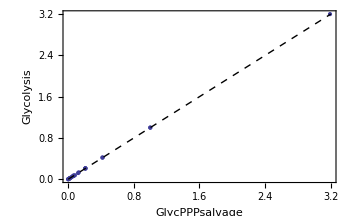

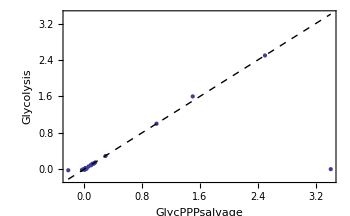

```mathematica
comparisonPlot@stripUnits[scatterFromDicts[combi["InitialConditions"],glycolysis["InitialConditions"]]]
comparisonPlot@stripUnits[scatterFromDicts[combi["InitialConditions"],ppp["InitialConditions"]]]
comparisonPlot@stripUnits[scatterFromDicts[combi["InitialConditions"],salvage["InitialConditions"]]]
```